```mathematica
(*with rfd, 5000 non interacting particles*)
(*SetDirectory[NotebookDirectory[]];
raw0=Import["0_asciiMeans000500000","Table"];
raw1=Import["1_asciiMeans000500000","Table"];
raw2=Import["2_asciiMeans000500000","Table"];.
raw3=Import["3_asciiMeans000500000","Table"];

raw=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]]];*)
steps=100;

SetDirectory[NotebookDirectory[]];
rawX=Table[Import["0_asciiEx00000"<>IntegerString[ii,10,4],"Table"][[1;;-3]],{ii,5,5*steps,5}];
rawY=Table[Import["0_asciiEy00000"<>IntegerString[ii,10,4],"Table"][[1;;-3]],{ii,5,5*steps,5}];
rawZ=Table[Import["0_asciiEz00000"<>IntegerString[ii,10,4],"Table"][[1;;-3]],{ii,5,5*steps,5}];
(*raw1=Import["1_asciiMeans000500000","Table"];*)
```

```mathematica
rawX
```

{$Failed⟦1;;-3⟧,198,{{(-4,-4,-4),2.39139×10^13},{(-3,-4,-4),2.07982×10^13},{(-2,-4,-4),9.53797×10^12},{(-1,-4,-4),-1.26516×10^12},6136,{(16,11,11),-4.86945×10^12},{(17,11,11),-9.01585×10^11},{(18,11,11),7.19186×10^12},{(19,11,11),1.35183×10^13}}}
 |  |  |  |

```mathematica
rawX[[1,1,2]]
```

1.1136×10^14

```mathematica
xs = 0.5*10^-5;
ys = 0.25*10^-5;
zs = 0.25*10^-5;
dx = xs/32;
dy = ys/16;
dz = zs/16;

convertX=Table[Table[{ToExpression[StringReplace[rawX[[jj,ii,1]],{"("-> "{",")"-> "}"}]],rawX[[jj,ii,2]]},{ii,1,Length[rawX[[jj]]]}],{jj,1,steps}];
convertXReal=Table[Table[{{convertX[[jj,ii,1,1]]*(dx)+dx/2,convertX[[jj,ii,1,2]]*(dy)+dy/2,convertX[[jj,ii,1,3]]*(dz)+dz/2},convertX[[jj,ii,2]]},{ii,1,Length[convertX[[jj]]]}],{jj,1,steps}];
func3Dx=Table[Interpolation[convertXReal[[jj]]],{jj,1,steps}];
```

```mathematica
convertY=Table[Table[{ToExpression[StringReplace[rawY[[jj,ii,1]],{"("-> "{",")"-> "}"}]],rawY[[jj,ii,2]]},{ii,1,Length[rawY[[jj]]]}],{jj,1,steps}];
convertYReal=Table[Table[{{convertY[[jj,ii,1,1]]*(dx)+dx/2,convertY[[jj,ii,1,2]]*(dy)+dy/2,convertY[[jj,ii,1,3]]*(dz)+dz/2},convertY[[jj,ii,2]]},{ii,1,Length[convertY[[jj]]]}],{jj,1,steps}];
func3Dy=Table[Interpolation[convertYReal[[jj]]],{jj,1,steps}];
```

```mathematica
convertZ=Table[Table[{ToExpression[StringReplace[rawZ[[jj,ii,1]],{"("-> "{",")"-> "}"}]],rawZ[[jj,ii,2]]},{ii,1,Length[rawZ[[jj]]]}],{jj,1,steps}];
convertZReal=Table[Table[{{convertZ[[jj,ii,1,1]]*(dx)+dx/2,convertZ[[jj,ii,1,2]]*(dy)+dy/2,convertZ[[jj,ii,1,3]]*(dz)+dz/2},convertZ[[jj,ii,2]]},{ii,1,Length[convertZ[[jj]]]}],{jj,1,steps}];
func3Dz=Table[Interpolation[convertZReal[[jj]]],{jj,1,steps}];
```

```mathematica
xx=1*dx;
yy=1*dy;
zz=1*dz;

func3Dx[[1]][xx,yy,zz]
func3Dy[[1]][xx,yy,zz]
func3Dz[[1]][xx,yy,zz]
```

2.99478×10^12

1.78521×10^12

-1.25939×10^13

```mathematica
pTab2D=Table[DensityPlot[((func3Dx[[jj]][x,y,zz])^2+(func3Dy[[jj]][x,y,zz])^2+(func3Dz[[jj]][x,y,zz])^2)^(1/2),{x,0,xs/2},{y,0,ys/2},ColorFunction->"TemperatureMap",AspectRatio->Automatic],{jj,1,steps}];
```

```mathematica
vTab2D=Table[VectorPlot[{func3Dx[[jj]][x,y,zz],func3Dy[[jj]][x,y,zz]},{x,0,xs/2},{y,0,ys/2},AspectRatio->Automatic],{jj,1,steps}];
```

```mathematica
aTab2D=Table[Show[pTab2D[[jj]],vTab2D[[jj]],Frame->False,ImageSize->2000],{jj,1,steps}];
```

```mathematica
ListAnimate[aTab2D];
```

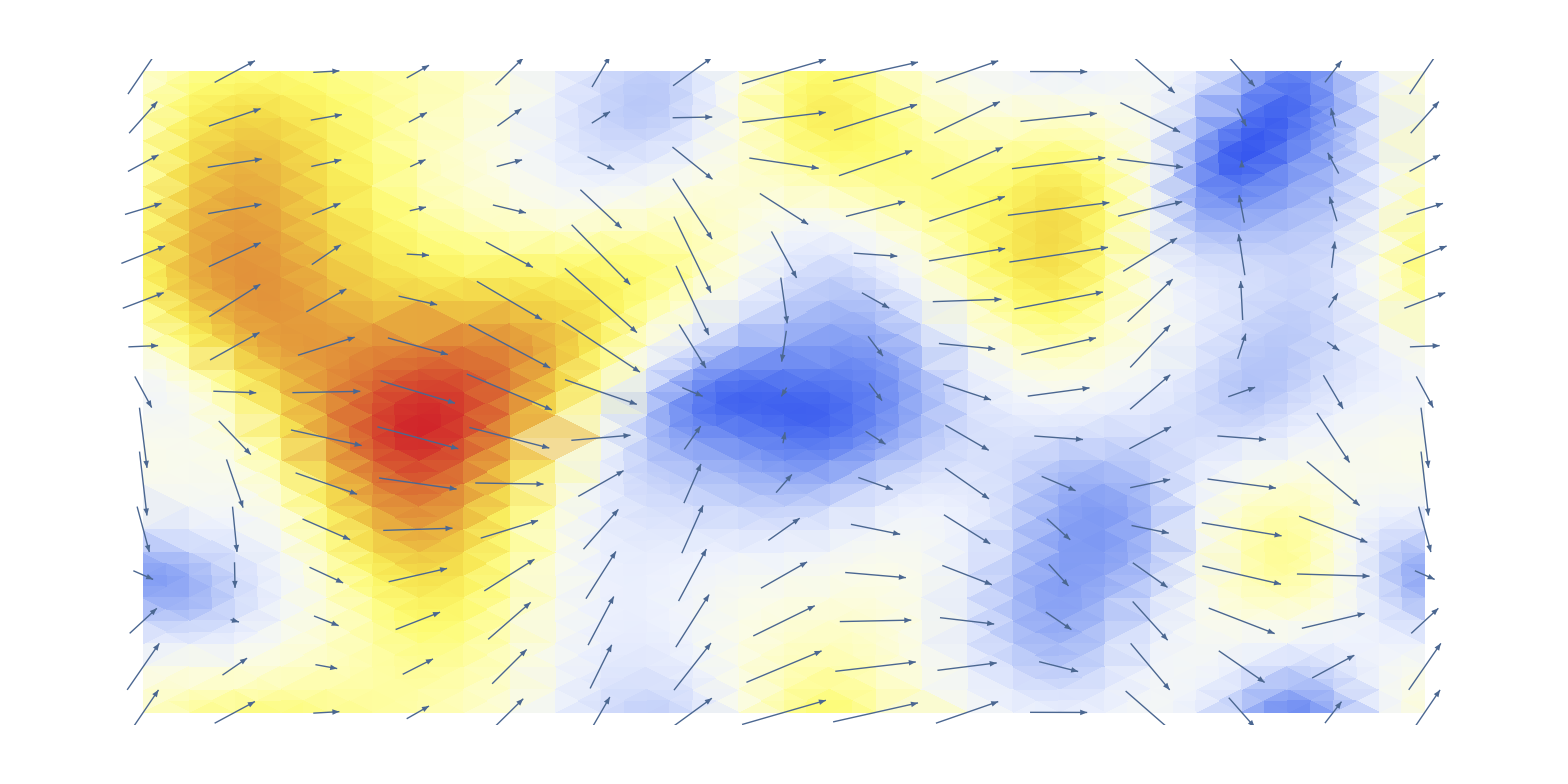

```mathematica
aTab2D[[1]]
```

```mathematica
For[ii=50,ii≤ steps,ii++,
Export["2d"<>IntegerString[ii,10,4]<>".jpg",aTab2D[[ii]],"CompressionLevel"->0];
];
```

```mathematica
aTab2D[[52]]
```

```mathematica
pTab1=Table[SliceDensityPlot3D[((func3Dx[[jj]][x,y,z])^2+(func3Dy[[jj]][x,y,z])^2+(func3Dz[[jj]][x,y,z])^2)^(1/2),{x,0,xs/4},{y,0,ys/4},{z,0,zs/2},ColorFunction->"TemperatureMap",AspectRatio->Automatic],{jj,1,steps}];
```

```mathematica
pTab2=Table[DensityPlot3D[((func3Dx[[jj]][x,y,z])^2+(func3Dy[[jj]][x,y,z])^2+(func3Dz[[jj]][x,y,z])^2)^(1/2),{x,0,xs/4},{y,0,ys/4},{z,0,zs/2},ColorFunction->"TemperatureMap",AspectRatio->Automatic,Boxed->False,Axes->False],{jj,1,steps}];
```

```mathematica
vTab=Table[VectorPlot3D[{func3Dx[[jj]][x,y,z],func3Dy[[jj]][x,y,z],func3Dz[[jj]][x,y,z]},{x,0,xs/2},{y,0,ys/2},{z,0,zs/2}],{jj,1,steps}];
```

```mathematica
aTab1=Table[Show[pTab2[[jj]],vTab[[jj]],Boxed->False,ImageSize->2000],{jj,1,steps}];
(*aTab2=Table[Show[pTab2[[jj]],parTab[[jj]],Boxed->False,ImageSize->2000],{jj,1,steps}];*)
```

```mathematica
ListAnimate[aTab1]
```

```mathematica
parTabP=Table[ListPointPlot3D[rawPp[[ii,All,1;;3]],PlotStyle->Red],{ii,1,steps}];
parTabN=Table[ListPointPlot3D[rawPn[[ii,All,1;;3]],PlotStyle->Blue],{ii,1,steps}];
parTab=Table[Show[parTabP[[ii]],parTabN[[ii]],Boxed->False,Axes->False],{ii,1,steps}];
```

Part::partd: Part specification rawPp⟦1,All,1;;3⟧ is longer than depth of object.

Part::pkspec1: The expression System`ListPointPlot3DDump`dataMinMax[1,1] cannot be used as a part specification.

Part::pkspec1: The expression System`ListPointPlot3DDump`dataMinMax[1,2] cannot be used as a part specification.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partd: Part specification rawPp⟦2,All,1;;3⟧ is longer than depth of object.

Part::pkspec1: The expression System`ListPointPlot3DDump`dataMinMax[2,1] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification rawPp⟦3,All,1;;3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rawPn⟦1,All,1;;3⟧ is longer than depth of object.

Part::pkspec1: The expression System`ListPointPlot3DDump`dataMinMax[1,1] cannot be used as a part specification.

Part::pkspec1: The expression System`ListPointPlot3DDump`dataMinMax[1,2] cannot be used as a part specification.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partd: Part specification rawPn⟦2,All,1;;3⟧ is longer than depth of object.

Part::pkspec1: The expression System`ListPointPlot3DDump`dataMinMax[2,1] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification rawPn⟦3,All,1;;3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ListAnimate[parTab]
```

```mathematica
For[ii=1,ii≤ steps,ii++,
Export["3d"<>IntegerString[ii,10,4]<>".jpg",aTab2[[ii]],"CompressionLevel"->0];
];
```

```mathematica
aTab2
```

{-Graphics3D-,-Graphics3D-}